```mathematica
Clear[model]
model[x0_,y0_,z0_] := {
x'[t] ==  x[t](1-x[t])-(a1 x[t] y[t])/(1 + b1 x[t]),
y'[t] == (a1 x[t] y[t])/(1 + b1 x[t])-(a2 y[t] z[t])/(1+b2 y[t])-d1 y[t],
z'[t] ==  (a2 y[t] z[t])/(1+b2 y[t])-d2 z[t],
x[0]==x0,
y[0]==y0,
z[0]==z0
};
```

```mathematica
param = {
a1->5.0,
a2->0.1,
b2->2.0,
d1->0.4,
d2->0.01
};
```

```mathematica
b1vals=Range[2.2,3.2,0.001];
bifTS=Table[NDSolve[model[0.8,0.2,10.0]/.param/.b1->b1val,{x,y,z},{t,0,10000},AccuracyGoal->8,PrecisionGoal->8], {b1val,b1vals}];//AbsoluteTiming
```

{50.6506,Null}

```mathematica
b1vals=Range[2.2,3.2,0.001];
bifTS=ParallelTable[NDSolve[model[0.8,0.2,10.0]/.param/.b1->b1val,{x,y,z},{t,0,10000},AccuracyGoal->8,PrecisionGoal->8], {b1val,b1vals}];//AbsoluteTiming
```

{20.2826,Null}

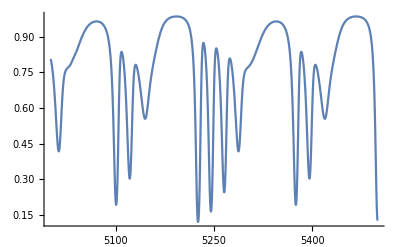

```mathematica
Plot[Evaluate[x[t]/.bifTS[[1000]]],{t, 5000,5500}]
```